```mathematica
ClearAll;
ClearCache;
```

```mathematica
SetDirectory["C:\Prime\Math_GGI"];
Get["GGIgeo.wl"]
```

```mathematica
(************************************************************************)
(************************************************************************)
(************************************************************************)
```

```mathematica
A11aV[a_] := A11aN[a].GravD[A11aX[a]]
A12aV[a_] := A12aN[a].GravD[A12aX[a]]
A13aV[a_] := A13aN[a].GravD[A13aX[a]]
A14aV[a_] := A14aN[a].GravD[A14aX[a]]
Bandpass[a_] := (A11aV[a] + A12aV[a]) - (A13aV[a] + A14aV[a])
```

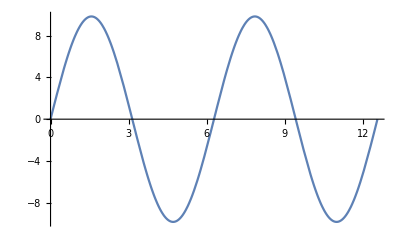

```mathematica
Plot[A11aV[a],{a,0,4π}]
```

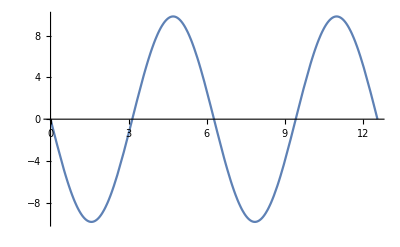

```mathematica
Plot[A12aV[a],{a,0,4π}]
```

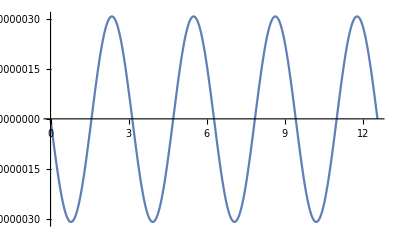

```mathematica
Plot[A11aV[a]+A12aV[a],{a,0,4π}]
```

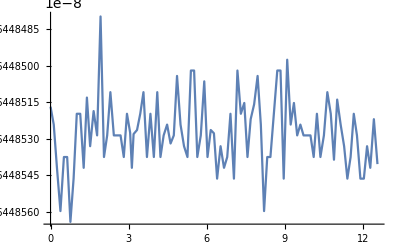

```mathematica
Plot[Bandpass[a],{a,0,4π}]
```

```mathematica
Bandpass[a]
```

-1.54173770848427810126530013356196291514647021260503604355504853806337293167711118229639862779987173×10^-6 (1+1.×10^-9 Cos[a]) Cos[a] (6.37101×10^6-2 Sin[a])+1.54173770848427810126530013356196291514647021260503604355504853806337293167711118229639862779987173×10^-6 (6.37101×10^6-2 Cos[a]) (1-1.×10^-9 Sin[a]) Sin[a]-1.54173770848427810126530013356196291514647021260503604355504853806337293167711118229639862779987173×10^-6 (6.37101×10^6+2 Cos[a]) (1+1.×10^-9 Sin[a]) Sin[a]+1.54173770848427810126530013356196291514647021260503604355504853806337293167711118229639862779987173×10^-6 (1-1.×10^-9 Cos[a]) Cos[a] (6.37101×10^6+2 Sin[a])

```mathematica
Precision[Bandpass[a]]
```

98.6835

```mathematica
FullSimplify[Bandpass[a]]
```

-1.9644852716260841251884479607849202704054626378417621367699299572974259162888384227044357243398522×10^-8+0. Cos[a]+0. Cos[2 a]+0. Cos[3 a]+0. Sin[a]+0. Cos[a] Sin[a]+0. Sin[3 a]

```mathematica
FullSimplify[Bandpass[a]==0]
```

False